```mathematica
data = Import["~/Documents/PhD-quali/zeca-analise/join_coun_prob.csv"]
```

{{AAA,1682,0.8244,0.},{AAC,185,0.6296,0.0242},{AAD,727,0.4844,0.074},{AAE,1000,0.6426,0.},{AAF,516,0.628,0.0976},{AAG,1246,0.5328,0.015},{AAH,350,0.5964,0.054},{AAI,764,0.445,0.0118},{AAK,761,0.6254,0.0136},7982,{YYN,124,0.595,0.0516},{YYP,121,0.3538,0.},{YYQ,92,0.3966,0.0838},{YYR,140,0.4638,0.1594},{YYS,136,0.442,0.121},{YYT,113,0.7814,0.035},{YYV,139,0.3854,0.048},{YYW,26,0.6568,0.},{YYY,105,0.3922,0.0714}}
 |  |  |  |

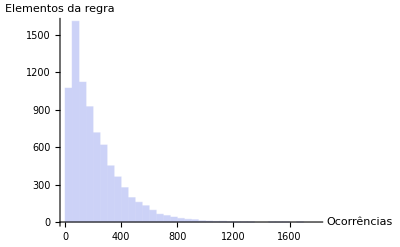

```mathematica
hist = Histogram[data[[All,2]], PlotRange->{{0,1800},{0,1600}}, PlotTheme->"Classic", AxesLabel-> {"Ocorrências", "Elementos da regra"}]
```

```mathematica
Export["~/Documents/PhD-quali/latex/quali/figures/histograma_occ.pdf", hist]
```

~/Documents/PhD-quali/latex/quali/figures/histograma_occ.pdf

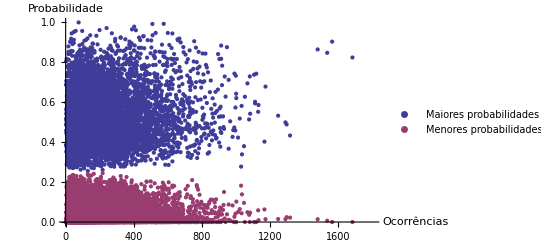

```mathematica
probG999=  ListPlot[{data[[All,{2,3}]], data[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", AxesLabel->{"Ocorrências","Probabilidade"}, PlotLegends->{"Maiores probabilidades", "Menores probabilidades"}]
```

```mathematica
Export["~/Documents/PhD-quali/latex/quali/figures/probG999_occXprob.pdf", probG999]
```

~/Documents/PhD-quali/latex/quali/figures/probG999_occXprob.pdf

```mathematica
Correlation[data[[All,2]], data[[All,3]]]
```

0.119164

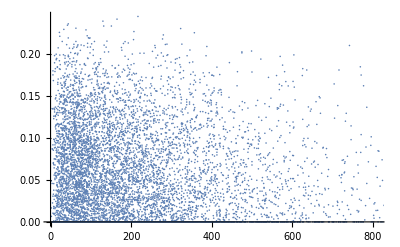

```mathematica
ListPlot[data[[All,{2,4}]]]
```

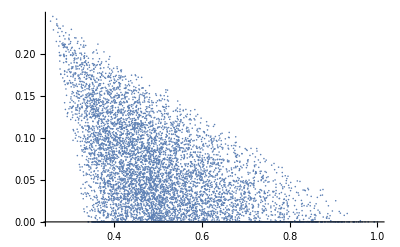

```mathematica
ListPlot[data[[All,{3,4}]]]
```

```mathematica
dataG10 = Import["~/zeca-analise/join_coun_prob_g10.csv"]
```

{{AAA,1682,0.277,0.2176},{AAC,185,0.2822,0.2234},{AAD,727,0.2654,0.224},{AAE,1000,0.2798,0.2222},{AAF,516,0.2964,0.2204},{AAG,1246,0.3144,0.215},{AAH,350,0.2688,0.2296},{AAI,764,0.2934,0.2098},{AAK,761,0.2892,0.208},{AAL,1534,0.309,0.2076},{AAM,374,0.2848,0.2286},{AAN,488,0.2656,0.2148},{AAP,498,0.2622,0.2184},{AAQ,561,0.276,0.2248},{AAR,903,0.2688,0.2264},7971,{YYH,53,0.282,0.2262},{YYI,105,0.2746,0.207},{YYK,134,0.2784,0.2238},{YYL,206,0.294,0.2152},{YYM,33,0.2664,0.2226},{YYN,124,0.2614,0.2456},{YYP,121,0.2764,0.2292},{YYQ,92,0.263,0.2358},{YYR,140,0.262,0.2248},{YYS,136,0.2684,0.23},{YYT,113,0.283,0.2108},{YYV,139,0.2582,0.2446},{YYW,26,0.305,0.2122},{YYY,105,0.2618,0.235}}
 |  |  |  |

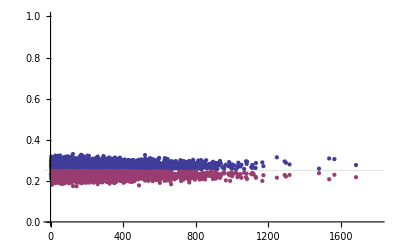

```mathematica
ListPlot[{dataG10[[All,{2,3}]],dataG10[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

```mathematica
dataG50 = Import["~/zeca-analise/join_coun_prob_g50.csv"]
```

{{AAA,1682,0.308,0.1542},{AAC,185,0.4118,0.14},{AAD,727,0.2936,0.2066},{AAE,1000,0.3622,0.1762},{AAF,516,0.3036,0.1616},{AAG,1246,0.3676,0.1724},{AAH,350,0.3316,0.1476},{AAI,764,0.31,0.178},{AAK,761,0.3666,0.2068},{AAL,1534,0.2706,0.2314},{AAM,374,0.2646,0.2338},{AAN,488,0.2976,0.205},{AAP,498,0.2588,0.2436},{AAQ,561,0.2978,0.2032},{AAR,903,0.2858,0.2088},7971,{YYH,53,0.321,0.2062},{YYI,105,0.3042,0.2104},{YYK,134,0.3438,0.1816},{YYL,206,0.3068,0.1956},{YYM,33,0.3228,0.1616},{YYN,124,0.318,0.2168},{YYP,121,0.2676,0.2224},{YYQ,92,0.2828,0.202},{YYR,140,0.2918,0.2158},{YYS,136,0.3332,0.2026},{YYT,113,0.2908,0.2044},{YYV,139,0.2844,0.2118},{YYW,26,0.3262,0.2032},{YYY,105,0.2802,0.1994}}
 |  |  |  |

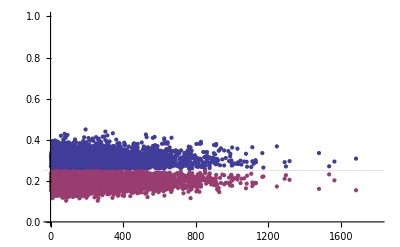

```mathematica
ListPlot[{dataG50[[All,{2,3}]],dataG50[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

```mathematica
dataG100 = Import["~/zeca-analise/join_coun_prob_g100.csv"]
```

{{AAA,1682,0.3478,0.134},{AAC,185,0.462,0.1328},{AAD,727,0.3262,0.2108},{AAE,1000,0.3752,0.1188},{AAF,516,0.3786,0.1744},{AAG,1246,0.299,0.2044},{AAH,350,0.3088,0.1232},{AAI,764,0.3554,0.127},{AAK,761,0.4626,0.1652},{AAL,1534,0.3368,0.1848},{AAM,374,0.3026,0.1882},{AAN,488,0.3036,0.1548},{AAP,498,0.3542,0.1462},{AAQ,561,0.3504,0.1786},{AAR,903,0.2968,0.1652},7971,{YYH,53,0.2672,0.228},{YYI,105,0.3314,0.1882},{YYK,134,0.3186,0.1704},{YYL,206,0.3216,0.1888},{YYM,33,0.3156,0.1452},{YYN,124,0.3086,0.1966},{YYP,121,0.2832,0.2026},{YYQ,92,0.3106,0.1792},{YYR,140,0.3128,0.1728},{YYS,136,0.3044,0.1676},{YYT,113,0.3236,0.1308},{YYV,139,0.2946,0.1938},{YYW,26,0.3058,0.2118},{YYY,105,0.3022,0.216}}
 |  |  |  |

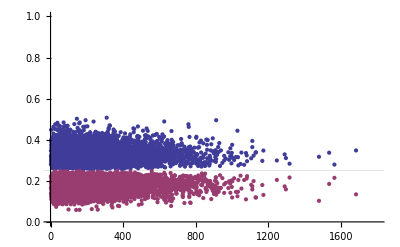

```mathematica
ListPlot[{dataG100[[All,{2,3}]],dataG100[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

```mathematica
dataG200 = Import["~/zeca-analise/join_coun_prob_g200.csv"]
```

{{AAA,1682,0.478,0.0684},{AAC,185,0.5338,0.1078},{AAD,727,0.3084,0.1906},{AAE,1000,0.4018,0.081},{AAF,516,0.3794,0.09},{AAG,1246,0.3336,0.165},{AAH,350,0.3426,0.1556},{AAI,764,0.3708,0.124},{AAK,761,0.4454,0.0884},{AAL,1534,0.3754,0.176},{AAM,374,0.3254,0.1584},{AAN,488,0.3864,0.1434},{AAP,498,0.3622,0.1352},{AAQ,561,0.4044,0.0988},{AAR,903,0.3782,0.111},7971,{YYH,53,0.2868,0.1762},{YYI,105,0.3466,0.1604},{YYK,134,0.3308,0.175},{YYL,206,0.3314,0.1716},{YYM,33,0.3568,0.1726},{YYN,124,0.3314,0.2038},{YYP,121,0.323,0.2066},{YYQ,92,0.2838,0.1734},{YYR,140,0.2992,0.205},{YYS,136,0.3052,0.2086},{YYT,113,0.4358,0.0556},{YYV,139,0.3418,0.1704},{YYW,26,0.3494,0.1832},{YYY,105,0.3112,0.1822}}
 |  |  |  |

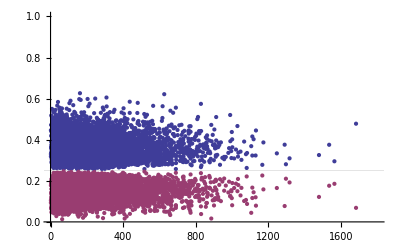

```mathematica
ListPlot[{dataG200[[All,{2,3}]],dataG200[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

```mathematica
dataG300 = Import["~/zeca-analise/join_coun_prob_g300.csv"];
```

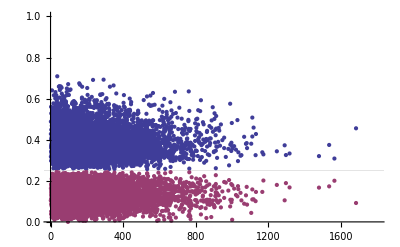

```mathematica
ListPlot[{dataG300[[All,{2,3}]],dataG300[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

```mathematica
dataG400 = Import["~/zeca-analise/join_coun_prob_g400.csv"];
```

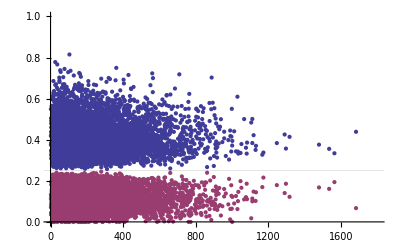

```mathematica
ListPlot[{dataG400[[All,{2,3}]],dataG400[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

```mathematica
dataG500 = Import["~/zeca-analise/join_coun_prob_g500.csv"];
```

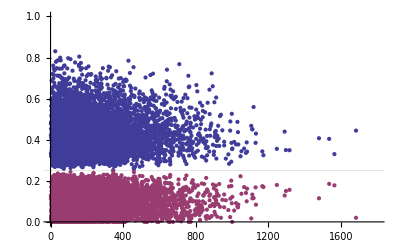

```mathematica
ListPlot[{dataG500[[All,{2,3}]],dataG500[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

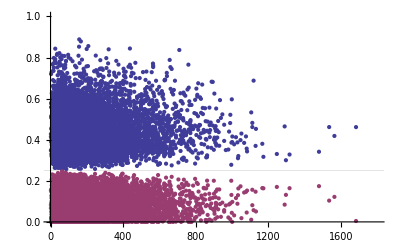

```mathematica
dataG600 = Import["~/zeca-analise/join_coun_prob_g600.csv"];
ListPlot[{dataG600[[All,{2,3}]],dataG600[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

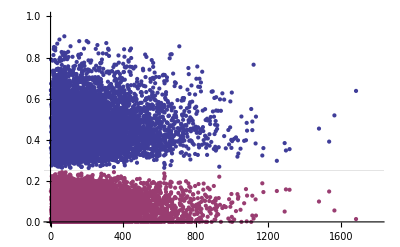

```mathematica
dataG700 = Import["~/zeca-analise/join_coun_prob_g700.csv"];
ListPlot[{dataG700[[All,{2,3}]],dataG700[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

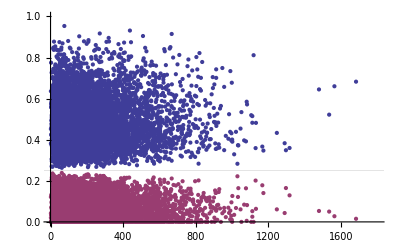

```mathematica
dataG800 = Import["~/zeca-analise/join_coun_prob_g800.csv"];
ListPlot[{dataG800[[All,{2,3}]],dataG800[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```

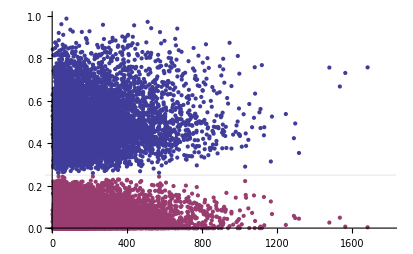

```mathematica
dataG900 = Import["~/zeca-analise/join_coun_prob_g900.csv"];
ListPlot[{dataG900[[All,{2,3}]],dataG900[[All,{2,4}]]}, PlotRange->{{0,1800},{0,1}}, PlotTheme->"Classic", GridLines->{{},{0.25}}]
```